```mathematica
OmegM=0.3;
OmegR=10^(-4);
H0=67;
```

{{y→InterpolatingFunction[…]}}

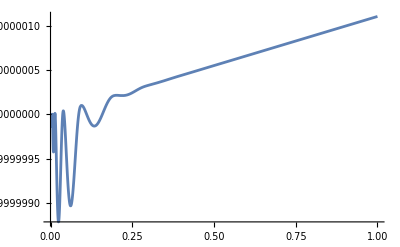

```mathematica
k=10^(-3) H0;
eq=y''[a]+(3/a-(3*OmegM/a+4*OmegR/a^2)/(2*(OmegM+OmegR/a))+(9*H0^2*(OmegM/a+OmegR/a^2))/(2*k^2)) y'[a]-(3/(2*a)) y[a]==0;
a0=10^-4;
ic={y[a0]==1,y'[a0]==0};
(*Numeric integration*)
sol1=NDSolve[{eq,ic},y,{a,a0,1},Method->{"StiffnessSwitching","NonstiffTest"->False}]
Plot[Evaluate[y[a]/. sol1],{a,a0,1}]
```

{{y→InterpolatingFunction[…]}}

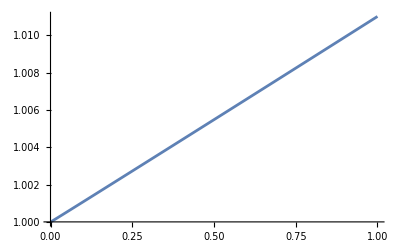

```mathematica
k=10^(-1) H0;
eq=y''[a]+(3/a-(3*OmegM/a+4*OmegR/a^2)/(2*(OmegM+OmegR/a))+(9*H0^2*(OmegM/a+OmegR/a^2))/(2*k^2)) y'[a]-(3/(2*a)) y[a]==0;
a0=10^-4;
ic={y[a0]==1,y'[a0]==0};
sol2=NDSolve[{eq,ic},y,{a,a0,1},Method->{"StiffnessSwitching","NonstiffTest"->False}]
Plot[Evaluate[y[a]/. sol2],{a,a0,1}]
```

{{y→InterpolatingFunction[…]}}

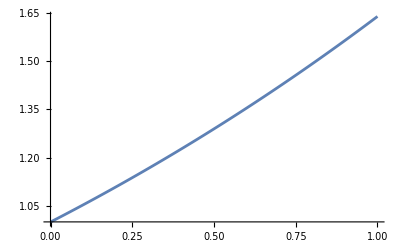

```mathematica
k= H0;
eq=y''[a]+(3/a-(3*OmegM/a+4*OmegR/a^2)/(2*(OmegM+OmegR/a))+(9*H0^2*(OmegM/a+OmegR/a^2))/(2*k^2)) y'[a]-(3/(2*a)) y[a]==0;
a0=10^-4;
ic={y[a0]==1,y'[a0]==0};
sol3=NDSolve[{eq,ic},y,{a,a0,1},Method->{"StiffnessSwitching","NonstiffTest"->False}]
Plot[Evaluate[y[a]/. sol3],{a,a0,1}]
```

{{y→InterpolatingFunction[…]}}

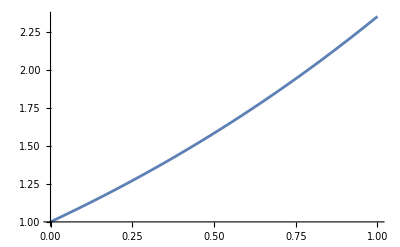

```mathematica
k= 100H0;
eq=y''[a]+(3/a-(3*OmegM/a+4*OmegR/a^2)/(2*(OmegM+OmegR/a))+(9*H0^2*(OmegM/a+OmegR/a^2))/(2*k^2)) y'[a]-(3/(2*a)) y[a]==0;
a0=10^-4;
ic={y[a0]==1,y'[a0]==0};
sol4=NDSolve[{eq,ic},y,{a,a0,1},Method->{"StiffnessSwitching","NonstiffTest"->False}]
Plot[Evaluate[y[a]/. sol4],{a,a0,1}]
```

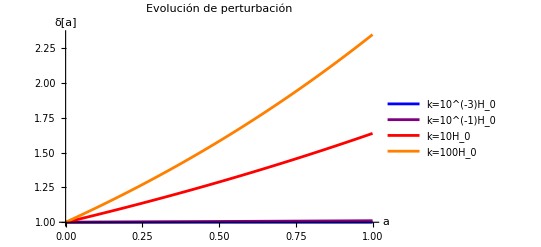

```mathematica
Plot1=Plot[Evaluate[y[a]/. sol1],{a,a0,1},AxesLabel->{"a","δ[a]"},PlotLabel->"Evolución de perturbación",PlotLegends->{"k=10^(-3)H_0"},PlotStyle->Blue];
Plot2=Plot[Evaluate[y[a]/. sol2],{a,a0,1},PlotLegends->{"k=10^(-1)H_0"},PlotStyle->Purple];
Plot3=Plot[Evaluate[y[a]/. sol3],{a,a0,1},PlotLegends->{"k=10H_0"},PlotStyle->Red];
Plot4=Plot[Evaluate[y[a]/. sol4],{a,a0,1},PlotLegends->{"k=100H_0"},PlotStyle->Orange];
Show[Plot1,Plot2,Plot3,Plot4,PlotRange->All]
```